This Mathematica code calculates various metrics for how virus within individuals evolves towards subtype-specific population consensus, and plots the figures

```mathematica
Needs["ErrorBarPlots`"]
```

File directories

```mathematica
patientSubtypesDir="pathname_here";(*directory of "Table S1.xlsx"*)
popSequencesDir="pathname_here";(*directory with the population level sequences*)
indivSequencesDir="pathname_here";(*directory with the individual level sequences*)
characterisedMutationsDir="pathname_here";
(*directory where the files characterising mutations are written to*);
patientsRemoved={"p1","p2","p4","p9","p12","p14","p20","p25","p34"};(*these are the patients with high diversity in p24 at the first time point*)
```

User defined functions

### Consensus[sequences_, i_]

Gives the consensus sequence at position i of given at set of sequences, where sequences is an nsite x nindiv table.

```mathematica
Consensus[sequences_,i_]:=Block[{nSeq, bases,temp,baseCount,noBase,cons},
nSeq=Length[sequences[All,i]];(*this gives the number of sequences*)
bases={"A","C","G","T"};
temp=sequences[[All,i]];(*this gives a list of the bases present in the population at locus i*)
baseCount=Count[temp,#]&/@bases; (*gives a list of how many As Cs, Gs and Ts there are at locus i*)
noBase=nSeq-Total[baseCount];(*number of sequences where no base is recorded (could be -, R, etc.)*)
cons=If[noBase>0.75nSeq,"-",bases[[Position[baseCount,Max[baseCount]]//Flatten]][[1]]];(*if => 3/4 of sequences don't have a base, then don't call the base, otherwise call it the most common base*)
Return[cons]]
```

### FindPopConsensus[region_, subtype_]

This finds the population consensus sequence given gene region and subtype

```mathematica
Clear[FindPopConsensus];
```

```mathematica
FindPopConsensus[region_,subtype_]:=FindPopConsensus[region,subtype]=Block[{suffix,seqs,nSequences,seqTab,nSites,popCon},

SetDirectory[];SetDirectory[popSequencesDir];

suffix=If[subtype=="A"||subtype=="D","_genbank_dated_20170309_patientaligned.fasta","_between_host_patientaligned.fasta"];

seqs=Import["subtype"<>subtype<>"_"<>region<>suffix,{"FASTA"}]; (*import the patient aligned sequences taken from genbank for the specified region and subtype*)

nSequences=Length[seqs];(*number of sequences imported*)

seqTab=Table[StringSplit[seqs[[i]],""],{i,nSequences}];(*create a table where each column is a nucleotide position and each row is for a different individual.  Entries are the base of the most sequence*)

nSites=Length[seqTab[[1]]];(*the number of sites in the imported sequences*)

popCon=Table[Consensus[seqTab,i],{i,1,nSites}];(*find the population consensus*)

SetDirectory[];

Return[popCon]]
```

### GapPos[region_]

Because of indels in gp41, we want to remove sites where there are gaps in most patients: The following finds the position of the indels (based on the first sequence in patient 1)

```mathematica
Clear[GapPos];
```

```mathematica
GapPos[region_]:=GapPos[region]=Block[{files,dat,firstSeq,gapPos},
If[region=="gp41",
SetDirectory[];SetDirectory[indivSequencesDir];(*change directory to where indiv data is*)
dat=Import["p1_gp41.fasta","FASTA"];(*import the sequences for patient p1*)
SetDirectory[];
firstSeq=StringSplit[dat[[1]],""]; (*find the first sequence and make the string into a list of bases. Note the first sequence will be the most common sequence at the first timepoint*)
gapPos=Position[firstSeq,"-"], (*find the position of the gaps: note, we don't flatten this list*)
gapPos={}];
Return[gapPos]]
```

### CodonPos[pos_]

Gives the nucleotide positions for the complete codon given a nucleotide position

```mathematica
CodonPos[pos_]:=Which[
Mod[pos,3]==1,{pos,pos+1,pos+2},
Mod[pos,3]==2,{pos-1,pos,pos+1},
Mod[pos,3]==0,{pos-2,pos-1,pos}]
```

### CodonToAA[codon_]

Given a codon (as a single string of 3 nucleotides) this gives the corresponding amino acid

```mathematica
CodonToAA[codon_]:=Block[{RNACodonTable},
RNACodonTable={
{"TTT","F"},
{"TTC","F"},
{"TTA","L"},
{"TTG","L"},
{"CTT","L"},
{"CTC","L"},
{"CTA","L"},
{"CTG","L"},
{"ATT","I"},
{"ATC","I"},
{"ATA","I"},
{"ATG","M"},
{"GTT","V"},
{"GTC","V"},
{"GTA","V"},
{"GTG","V"},
{"TCT","S"},
{"TCC","S"},
{"TCA","S"},
{"TCG","S"},
{"CCT","P"},
{"CCC","P"},
{"CCA","P"},
{"CCG","P"},
{"ACT","T"},
{"ACC","T"},
{"ACA","T"},
{"ACG","T"},
{"GCT","A"},
{"GCC","A"},
{"GCA","A"},
{"GCG","A"},
{"TAT","Y"},
{"TAC","Y"},
{"TAA","Stop"},
{"TAG","Stop"},
{"CAT","H"},
{"CAC","H"},
{"CAA","Q"},
{"CAG","Q"},
{"AAT","N"},
{"AAC","N"},
{"AAA","K"},
{"AAG","K"},
{"GAT","D"},
{"GAC","D"},
{"GAA","E"},
{"GAG","E"},
{"TGT","C"},
{"TGC","C"},
{"TGA","Stop"},
{"TGG","W"},
{"CGT","R"},
{"CGC","R"},
{"CGA","R"},
{"CGG","R"},
{"AGT","S"},
{"AGC","S"},
{"AGA","R"},
{"AGG","R"},
{"GGT","G"},
{"GGC","G"},
{"GGA","G"},
{"GGG","G"}};
Select[RNACodonTable,#[[1]]==codon&][[1,2]]
];
```

### CharMutsPolySites[patient_, region_, consThreshold_, freqThreshold_, transitionBias_]

For a specific patient-region combination, and ts:tv ratio: For polymorphic sites (defined as those where the most common allele is >conThreshold in frequency at the first sampling time point, but where a minor allele is >freqThreshold frequency at a later time point), this gives a table listing: {patient id, gene region, subtype, time point, locus, AS, ANS, TS, TNS, XS, XNS, E[AS], E[ANS], E[TS], E[TNS], E[XS], E[XNS], NCS (number of nonconsensus sites), NCSsynon (numberof nonconsensus sites, synonymous), NCSnonsynon (number of nonconsensus sites, nonsynon)}, where A = number of changes away from consensus, T = to consensus, X = was away and stayed away from consensus, S = synonymous, NS = nonsynonymous, and E[] refers to the expected number.

```mathematica
CharMutsPolySites[patient_,region_,consThreshold_,freqThreshold_,transitionBias_]:=Block[{subtypeDat,subtype,dat,names,seqs,dates,stamps,nStamps,gapPos,popCon,nSites,repeats,seqTab,bases,baseTot,baseFreq,baseFreqChange,ancestralFreq,ancestralIndex,ancestralSeq,posCon,NCS,NCC,NCAncestralCodons,NCConsensusCodons,NCAncestralAA,NCConsensusAA,nSitesNC,nSitesNCSynon,nSitesNCNonsynon,output,maxChange,posChange,polySites,baseIndexChange,newBase,ancestralBase,consensusBase,potentialNewBase,potentialNewBase1,potentialNewBase2,codonPos,ancestralCodons,newCodons,consensusCodons,potentialNewCodons1,potentialNewCodons2,ancestralAA,newAA,potentialNewAA1,potentialNewAA2,summary,potentialSummary1,newBaseRate,potentialSummary2,potentialBase1Rate,potentialBase2Rate,expectedOutDat,totRate},

Off[Power::infy];
Off[Infinity::indet];

SetDirectory[];SetDirectory[patientSubtypesDir];
subtypeDat=Import["Table S1.xlsx"][[1,2;;,{1,4,5}]];(*import the subtype data for each region/patient*)
subtype=Extract[subtypeDat[[;;,If[region=="gag",2,3]]],Position[subtypeDat[[;;,1]],patient][[1]]];(*this gives the subtype of the patient-region we are interested in*)

SetDirectory[];SetDirectory[indivSequencesDir];
dat=Import[patient<>"_"<>region<>".fasta",{"FASTA","Data"}];(*import the patient sequence data*)
names=dat[[1]];(*extracts the seqeunce names*)
seqs=dat[[2]];(*this gives the sequence of each sequence*)
dates=ToExpression[StringSplit[#,"_"][[5]]&/@names];(*this gives the time stamp of each sequence*)
stamps=Sort[DeleteDuplicates[dates],#2>#1&];(*a list of the timestamps in increasing order*)
nStamps=Length[stamps];(*the number of time stamps*)
gapPos=GapPos[region];(*positions to remove due to indels*)
popCon=Delete[FindPopConsensus[region,subtype],gapPos];(*the population consensus for the region-subtype we are interested in. We remove sites where indels are common in the Rakai patients*)
nSites=Length[popCon];(*the number of sites at the population consensus*)
repeats=ToExpression[StringSplit[#,"_"][[3]]&/@names];(*this gives the number of repeats of each sequence*)
seqTab=Table[Delete[DeleteCases[StringSplit[seqs[[i]],""]," "],gapPos],{i,Length[seqs]}][[All,1;;Length[popCon]]];(*a table where each column is a site position and each row a unique sequence and each entry in the base found.  If there are a blank spaces at the beginning or ending of the sequences then these are deleted, and then the previously identified gaps are also deleted.  Finally, only the first n sites are chosen, where n is the length of the consensus sequence*)

bases={"A","C","G","T","-"};baseTot=Table[repeats[[Intersection[Position[dates,stamps[[t]]],Position[seqTab[[All,i]],bases[[b]]]]//Flatten]]//Total,{t,nStamps},{b,4},{i,nSites}];(*an nStamps x 4 x nSites array giving the number of A,C,G and Ts at each position and each timepoint*)baseFreq=Table[baseTot[[t,b]]/Total[baseTot[[t]]]//N,{t,nStamps},{b,4}];(*an nStamps x 4 x nSites array giving the frequency of A,C,G and Ts at each position and each timepoint. NB This will be 'Indeterminate' if have all zeros at a site at the first timepoint*)baseFreqChange=Table[baseFreq[[t]]-baseFreq[[1]],{t,2,nStamps}];
(*an nStamps-1 x 4 x nSites array giving the change in frequency of A,C,G and T between the first and t+1'th timepoint*)

ancestralFreq=Max/@(baseFreq[[1]]//Transpose);ancestralFreq=ancestralFreq/.Indeterminate->"NA";(*this gives the frequency of the highest frequenccy base at the first timepoint for each site. We do the replacement, otherwise at inderterminate sites we are matching Indeterminate in each of the base frequences with Indeterminate in the ancestral frequency, which can throw everything off*)

ancestralIndex=MapThread[Position,{baseFreq[[1]]//Transpose,ancestralFreq}]/.{}->{{5}}//Flatten;
(*the base index (1,2,3 or 4) for each site of the consensus at the first timepoint. For sites where there is no match, we put "-" instead of a base*)

ancestralSeq=bases[[ancestralIndex]];(*the ancestral consensus sequences at the first timepoint*)
posCon=Position[ancestralFreq,n_/;n≥consThreshold]//Flatten;(*positions where the frequency of the ancestral consensus is ≥ consThreshold*)

NCS=Select[Position[MapThread[(#1!=#2)&&(#1≠"-")&&(#2≠"-")&,{popCon,ancestralSeq}],True]//Flatten,#≤3 IntegerPart[nSites/3]&];(*Non Consensus Sites: Sites where the ancestral consensus sequence differs to the population consensus sequence. We remove "-" sites and only use sites where we have a complete codon*)
NCC=CodonPos/@NCS;(*Non Consensus Codon: The nucleotide indexes for the three nucleotides associated with the codon in which an ancestral consensus differs from the population consensus*)

NCAncestralCodons=Map[ancestralSeq[[#]]&,NCC];(*The bases associated with the NCCs in the ancestral consensus sequence*)
NCConsensusCodons=Map[popCon[[#]]&,NCC];(*The bases associated with the NCCs in the population consensus sequence*)
NCAncestralAA=CodonToAA/@(StringJoin/@NCAncestralCodons);(*ancestral consensus amino acid for sites where ancestral ≠ population consensus at the nucleotide level.  i.e the amino acids might be the same*)
NCConsensusAA=CodonToAA/@(StringJoin/@NCConsensusCodons);(*population consensus amino acid for sites where ancestral ≠ population consensus at the nucleotide level*)
nSitesNC=Length[NCS];(*number of sites where consensus ≠ ancester*)
nSitesNCSynon=Count[MapThread[#1==#2&,{NCAncestralAA,NCConsensusAA}],True];(*number of sites where consensus ≠ ancester and the difference is synonymous*)
nSitesNCNonsynon=nSitesNC-nSitesNCSynon;(*number of sites where consensus ≠ ancester and the difference is nonsynonymous*)

(*output={{
patient,
region,
subtype,
stamps[[1]],
"ancestral",
Table[0,{12}],
nSitesNC, nSitesNCSynon,nSitesNCNonsynon}//Flatten};*)
output={};

(*we now loop over each of the time stamps, to find the summary statistics for changes towards consensus, away from consensus, and staying away from consensus, and the expected changes assuming changes can only occur at polymorphic sites*)

For[tt=1,tt<nStamps,tt++,
maxChange=Max/@(baseFreqChange[[tt]]//Transpose);(*the maximum base frequency change at each site between the first and timeindex[[tt]]'th timepoint*)
posChange=Position[maxChange,n_/;n≥ freqThreshold]//Flatten;(*a list of sites where bases have changed by more that freqthreshold frequency*)

polySites=Select[Intersection[posChange,posCon],#≤3 IntegerPart[nSites/3]&];(*Polymorphic sites: the site indexes where the ancestral consensus is ≥ consThreshold, where a single base has increased by > freqThreshold, and where the site is part of a complete codon, for the time point stamps[[timeindex[[tt]]]]*)

If[Length[polySites]>0,(*If needed for case where no loci fit critia of near fixation at the first timepoint and minor allele increased >freqThreshold at at least one of the timepoints we are interested in*)

baseIndexChange=MapThread[Position,{baseFreqChange[[tt,All,polySites]]//Transpose,maxChange[[polySites]]}]//Flatten;(*index of the base that has increased in frequency ie. A, C, G or T, at the polymorphic sites*)

newBase=bases[[baseIndexChange]];(*new bases at the polymorphic sites*)
ancestralBase=ancestralSeq[[polySites]];(*ancestral bases at the polymorphic sites*)
consensusBase=popCon[[polySites]];(*populations consensus bases at the polymorphic sites*)

potentialNewBase=MapThread[Complement[bases[[1;;4]],{#1,#2}]&,{ancestralBase,newBase}]//Transpose;
potentialNewBase1=potentialNewBase[[1]];(*these are althernative base changes that could have occured at polymorphic sites*)
potentialNewBase2=potentialNewBase[[2]];(*these are althernative base changes that could have occured at polymorphic sites*)

codonPos=CodonPos/@polySites;(*the nucleotide indexes for the three nucleotides associated with the AA at polymorphic sites*)
ancestralCodons=Map[ancestralSeq[[#]]&,codonPos];(*the complete codon for the ancestral consensus at polymorphic sites*)
newCodons=MapThread[ReplacePart[#1,Position[#2,#3][[1,1]]->#4]&,{ancestralCodons,codonPos,polySites,newBase}];(*the new codons at polymorphic sites*)
consensusCodons=Map[popCon[[#]]&,codonPos];(*the population consensus codons at polymorphic sites*)

potentialNewCodons1=MapThread[ReplacePart[#1,Position[#2,#3][[1,1]]->#4]&,{ancestralCodons,codonPos,polySites,potentialNewBase1}];
potentialNewCodons2=MapThread[ReplacePart[#1,Position[#2,#3][[1,1]]->#4]&,{ancestralCodons,codonPos,polySites,potentialNewBase2}];
ancestralAA=CodonToAA/@(StringJoin/@ancestralCodons);(*the ancestral amino acid at polymorphic sites*)
newAA=CodonToAA/@(StringJoin/@newCodons);(*the new amino acid at polymorphic sites*)
potentialNewAA1=CodonToAA/@(StringJoin/@potentialNewCodons1);(*alternative AAs at polymorphic sites if there had been an alternative base change*)
potentialNewAA2=CodonToAA/@(StringJoin/@potentialNewCodons2);(*alternative AAs at polymorphic sites if there had been an alternative base change*)

summary=MapThread[Which[
#1==#2&&#3==#4,"AS",
#1==#2 &&#3≠#4,"ANS",
#5==#2 &&#3==#4,"TS",
#5==#2&&#3≠#4,"TNS",
#1≠#2&&#3==#4,"XS",
#1≠#2&&#3!=#4,"XNS"]&,{ancestralBase,consensusBase,ancestralAA,newAA,newBase}];(*this gives a list characterising the changes at the polymorphic sites: A = away from consensus, T = to consensus, X = was away and stayed away from consensus, S = synonymous, NS = nonsynonymous*)

potentialSummary1=MapThread[Which[
(*#4=="Stop","D",*)
#1==#2&&#3==#4,"AS",
#1==#2 &&#3≠#4,"ANS",
#5==#2 &&#3==#4,"TS",
#5==#2&&#3≠#4,"TNS",
#1≠#2&&#3==#4,"XS",
#1≠#2&&#3!=#4,"XNS"]&,{ancestralBase,consensusBase,ancestralAA,potentialNewAA1,potentialNewBase1}];

potentialSummary2=MapThread[Which[
(*#4=="Stop","D",*)
#1==#2&&#3==#4,"AS",
#1==#2 &&#3≠#4,"ANS",
#5==#2 &&#3==#4,"TS",
#5==#2&&#3≠#4,"TNS",
#1≠#2&&#3==#4,"XS",
#1≠#2&&#3!=#4,"XNS"]&,{ancestralBase,consensusBase,ancestralAA,potentialNewAA2,potentialNewBase2}];

newBaseRate=MapThread[If[
#1=="G"&&#2=="A"||#1=="A"&&#2=="G"||#1=="C"&&#2=="T"||#1=="T"&&#2=="C", 2 transitionBias,1]&,{ancestralBase,newBase}];(*assuming a transversion has rate 1, this gives the rate of seeing the given base change, assuming the given transition bias*)

potentialBase1Rate=MapThread[Which[
#3=="D",0,
#1=="G"&&#2=="A"||#1=="A"&&#2=="G"||#1=="C"&&#2=="T"||#1=="T"&&#2=="C",2 transitionBias,
#3≠"D",1]&,{ancestralBase,potentialNewBase1,potentialSummary1}];(*as above, but for the alternative changes.  If this would lead to a stop codon, it is given rate 0, if included in teh potential summaries above*)

potentialBase2Rate=MapThread[Which[
#3=="D",0,
#1=="G"&&#2=="A"||#1=="A"&&#2=="G"||#1=="C"&&#2=="T"||#1=="T"&&#2=="C",2transitionBias,
#3≠"D",1]&,{ancestralBase,potentialNewBase2,potentialSummary2}];
(*as above, but for the alternative changes.  If this would lead to a stop codon, it is given rate 0, if included in teh potential summaries above*)

totRate=Total[{newBaseRate,potentialBase1Rate,potentialBase2Rate}];(*sum of the rates of changes at polymorphic sites, not accounting for stop codons - but this can be included by altering potentialsummary1 and potentialsummary2*)

(*for each row, output gives patientid, subtype, timestamp, locus, then number of {"AS","ANS","TS","TNS","XS","XNS"} mutations followed by exptected number of {"AS","ANS","TS","TNS","XS","XNS"} mutations, and finally the number of non consensus sites for all, synonymous and nonsynonyous mutations*)

output=Join[output,Table[{
patient,
region,
subtype,
stamps[[tt+1]],
polySites[[siteindex]],
Map[Boole[summary[[siteindex]]==#]&,{"AS","ANS","TS","TNS","XS","XNS"}],
Map[Boole[summary[[siteindex]]==#]newBaseRate[[siteindex]]/totRate[[siteindex]]+Boole[potentialSummary1[[siteindex]]==#]potentialBase1Rate[[siteindex]]/totRate[[siteindex]]+Boole[potentialSummary2[[siteindex]]==#]potentialBase2Rate[[siteindex]]/totRate[[siteindex]]&,{"AS","ANS","TS","TNS","XS","XNS"}],
nSitesNC, nSitesNCSynon,nSitesNCNonsynon}//Flatten,{siteindex, Length[polySites]}]
]]; 
];

SetDirectory[];
On[Power::infy];
On[Infinity::indet];
Return[output]]
```

### CharMutsAllSites[patient_, region_, consThreshold_, freqThreshold_, transitionBias_]

For a given patient-region combination and a specific ts:tv ration: For all sites , this gives a table listing: {patient id, gene region, subtype, E[AS], E[ANS], E[TS], E[TNS], E[XS], E[XNS]}, where A = changes away from consensus, T = to consensus, X = was away and stayed away from consensus, S = synonymous, NS = nonsynonymous, and E[] refers to the expected proportion, given that mutation occurs.

```mathematica
CharMutsAllSites[patient_,region_,consThreshold_,freqThreshold_,transitionBias_]:=Block[{subtypeDat,subtype,dat,names,seqs,dates,stamps,nStamps,gapPos,popCon,nSites,repeats,seqTab,bases,baseTot,baseFreq,ancestralFreq,ancestralIndex,ancestralSeq,posNoCodonInfo,posCon,allSites,ancestralBase,consensusBase,potentialNewBase,potentialNewBase1,potentialNewBase2,potentialNewBase3,codonPos,ancestralCodons,consensusCodons,potentialNewCodons1,potentialNewCodons2,potentialNewCodons3,ancestralAA,potentialNewAA1,potentialNewAA2,potentialNewAA3,summary1, summary2,summary3,potentialBase1Rate,potentialBase2Rate,potentialBase3Rate,totRate,tab,output
},

Off[Power::infy];
Off[Infinity::indet];

SetDirectory[];SetDirectory[patientSubtypesDir];
subtypeDat=Import["Table S1.xlsx"][[1,2;;,{1,4,5}]];(*import the subtype data for each region/patient*)
subtype=Extract[subtypeDat[[;;,If[region=="gag",2,3]]],Position[subtypeDat[[;;,1]],patient][[1]]];(*this gives the subtype of the patient-region we are interested in*)

SetDirectory[];SetDirectory[indivSequencesDir];
dat=Import[patient<>"_"<>region<>".fasta",{"FASTA","Data"}];(*import the patient sequence data*)
names=dat[[1]];(*extracts the seqeunce names*)
seqs=dat[[2]];(*this gives the sequence of each sequence*)
dates=ToExpression[StringSplit[#,"_"][[5]]&/@names];(*this gives the time stamp of each sequence*)
stamps=Sort[DeleteDuplicates[dates],#2>#1&];(*a list of the timestamps in increasing order*)
nStamps=Length[stamps];(*the number of time stamps*)
gapPos=GapPos[region];(*positions to remove due to indels*)
popCon=Delete[FindPopConsensus[region,subtype],gapPos];(*the population consensus for the region-subtype we are interested in. We remove sites where indels are common in the Rakai patients*)
nSites=Length[popCon];(*the number of sites at the population consensus*)
repeats=ToExpression[StringSplit[#,"_"][[3]]&/@names];(*this gives the number of repeats of each sequence*)
seqTab=Table[Delete[DeleteCases[StringSplit[seqs[[i]],""]," "],gapPos],{i,Length[seqs]}][[All,1;;Length[popCon]]];(*a table where each column is a site position and each row a unique sequence and each entry in the base found.  If there are a blank spaces at the beginning or ending of the sequences then these are deleted, and then the previously identified gaps are also deleted.  Finally, only the first n sites are chosen, where n is the length of the consensus sequence*)

bases={"A","C","G","T","-"};baseTot=Table[repeats[[Intersection[Position[dates,stamps[[t]]],Position[seqTab[[All,i]],bases[[b]]]]//Flatten]]//Total,{t,nStamps},{b,4},{i,nSites}];(*an nStamps x 4 x nSites array giving the number of A,C,G and Ts at each position and each timepoint*)baseFreq=Table[baseTot[[t,b]]/Total[baseTot[[t]]]//N,{t,nStamps},{b,4}];(*an nStamps x 4 x nSites array giving the frequency of A,C,G and Ts at each position and each timepoint. NB This will be 'Indeterminate' if have all zeros at a site at the first timepoint*)

ancestralFreq=Max/@(baseFreq[[1]]//Transpose);ancestralFreq=ancestralFreq/.Indeterminate->"NA";(*this gives the frequency of the highest frequenccy base at the first timepoint for each site. We do the replacement, otherwise at inderterminate sites we are matching Indeterminate in each of the base frequences with Indeterminate in the ancestral frequency, which can throw everything off*)

ancestralIndex=MapThread[Position,{baseFreq[[1]]//Transpose,ancestralFreq}]/.{}->{{5}}//Flatten;
(*the base index (1,2,3 or 4) for each site of the consensus at the first timepoint. For sites where there is no match, we put "-" instead of a base*)

ancestralSeq=bases[[ancestralIndex]];(*the ancestral consensus sequences at the first timepoint*)
posNoCodonInfo=CodonPos/@Flatten[Position[ancestralSeq,"-"]]//Flatten;(*sites for which we can't determine the ancestral codon*)
posCon=Position[ancestralFreq,n_/;n≥consThreshold]//Flatten;(*positions where the frequency of the ancestral consensus is ≥ consThreshold*)

allSites=Complement[Select[posCon,#≤3 IntegerPart[nSites/3]&],posNoCodonInfo];(*loci where individual consensus is ≥ consThreshold and where the locus is part of a complete codon at the first timepoint*)

ancestralBase=ancestralSeq[[allSites]];(*ancestral base for the sites we are interested in*)
consensusBase=popCon[[allSites]];(*consensus base for the sites we are interested in*)
potentialNewBase=Map[Complement[bases[[1;;4]],{#}]&,ancestralBase]//Transpose;(*tthe alternative bases that could occur at these sites*)
potentialNewBase1=potentialNewBase[[1]];
potentialNewBase2=potentialNewBase[[2]];
potentialNewBase3=potentialNewBase[[3]];

codonPos=CodonPos/@allSites;(*the nucleotide indexes for the three nucleotides associated with the AA in which there has been a nucleotide change*)

ancestralCodons=Map[ancestralSeq[[#]]&,codonPos];(*the complete codon for the individual consensus*)
consensusCodons=Map[popCon[[#]]&,codonPos];(*the population consensus codon*)

potentialNewCodons1=MapThread[ReplacePart[#1,Position[#2,#3][[1,1]]->#4]&,{ancestralCodons,codonPos,allSites,potentialNewBase1}];
potentialNewCodons2=MapThread[ReplacePart[#1,Position[#2,#3][[1,1]]->#4]&,{ancestralCodons,codonPos,allSites,potentialNewBase2}];
potentialNewCodons3=MapThread[ReplacePart[#1,Position[#2,#3][[1,1]]->#4]&,{ancestralCodons,codonPos,allSites,potentialNewBase3}];
	
ancestralAA=CodonToAA/@(StringJoin/@ancestralCodons);(*ancestral amino acid for all nucleotide sites*)
potentialNewAA1=CodonToAA/@(StringJoin/@potentialNewCodons1);(*potential amino acid if there was a mutations for all nucleotide sites*)
potentialNewAA2=CodonToAA/@(StringJoin/@potentialNewCodons2);(*potential amino acid if there was a mutations for all nucleotide sites*)
potentialNewAA3=CodonToAA/@(StringJoin/@potentialNewCodons3);(*potential amino acid if there was a mutations for all nucleotide sites*)

summary1=MapThread[Which[
(*#4=="Stop","D",*)
#1==#2&&#3==#4,"AS",
#1==#2 &&#3≠#4,"ANS",
#5==#2 &&#3==#4,"TS",
#5==#2&&#3≠#4,"TNS",
#1≠#2&&#3==#4,"XS",
#1≠#2&&#3!=#4,"XNS"]&,{ancestralBase,consensusBase,ancestralAA,potentialNewAA1,potentialNewBase1}];(*list characterising the potential mutations A = away from consensus, T = to consensus, X = was away and stayed away from consensus, S = synonymous, NS = nonsynonymous, for the first potential mutation*)

summary2=MapThread[Which[
(*#4=="Stop","D",*)
#1==#2&&#3==#4,"AS",
#1==#2 &&#3≠#4,"ANS",
#5==#2 &&#3==#4,"TS",
#5==#2&&#3≠#4,"TNS",
#1≠#2&&#3==#4,"XS",
#1≠#2&&#3!=#4,"XNS"]&,{ancestralBase,consensusBase,ancestralAA,potentialNewAA2,potentialNewBase2}];

summary3=MapThread[Which[
(*#4=="Stop","D",*)
#1==#2&&#3==#4,"AS",
#1==#2 &&#3≠#4,"ANS",
#5==#2 &&#3==#4,"TS",
#5==#2&&#3≠#4,"TNS",
#1≠#2&&#3==#4,"XS",
#1≠#2&&#3!=#4,"XNS"]&,{ancestralBase,consensusBase,ancestralAA,potentialNewAA3,potentialNewBase3}];

potentialBase1Rate=MapThread[Which[
#3=="D",0,
#1=="G"&&#2=="A"||#1=="A"&&#2=="G"||#1=="C"&&#2=="T"||#1=="T"&&#2=="C",2transitionBias,
#3≠"D",1]&,{ancestralBase,potentialNewBase1,summary1}];
(*assuming a transversion has rate 1, this gives the rate of seeing the given base change, assuming the given transition bias*)

potentialBase2Rate=MapThread[Which[
#3=="D",0,
#1=="G"&&#2=="A"||#1=="A"&&#2=="G"||#1=="C"&&#2=="T"||#1=="T"&&#2=="C",2transitionBias,
#3≠"D",1]&,{ancestralBase,potentialNewBase2,summary2}];

potentialBase3Rate=MapThread[Which[
#3=="D",0,
#1=="G"&&#2=="A"||#1=="A"&&#2=="G"||#1=="C"&&#2=="T"||#1=="T"&&#2=="C",2transitionBias,
#3≠"D",1]&,{ancestralBase,potentialNewBase3,summary3}];

totRate=Total[{potentialBase1Rate,potentialBase2Rate,potentialBase3Rate}];(*sum of the rates of changes at polymorphic sites, not accounting for stop codons - but this can be included by altering summary1, summary2, summary3*)

tab=Table[
Map[Boole[summary1[[siteindex]]==#]potentialBase1Rate[[siteindex]]/totRate[[siteindex]]+Boole[summary2[[siteindex]]==#]potentialBase2Rate[[siteindex]]/totRate[[siteindex]]+Boole[summary3[[siteindex]]==#]potentialBase3Rate[[siteindex]]/totRate[[siteindex]]&,{"AS","ANS","TS","TNS","XS","XNS"}],{siteindex, Length[allSites]}];(*for each locus, this gives the expected proportion of mutations that AS, ANS, TS, TNS, XS and XNS, given mutation does occur*)

output={
patient,
region,
subtype,
tab//Total//N}//Flatten;

SetDirectory[];
On[Power::infy];
On[Infinity::indet];
Return[output]]
```

### Bootstrap[list_]

Performs one bootstrap on a given list

```mathematica
Bootstrap[list_]:=RandomChoice[list,Length[list]];
```

### PositionDuplicates[list_]

```mathematica
PositionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&]
```

### ToConsensusStats[polyDat_, allDat_, region_, datMin_, datMax_, nBootstraps_]

This produces the statistics we are interested in, including 5% and 95% confidence intervals based on bootstrapping the data at the patient level. The output is a table where each row gives {toBias, toSBias, toNSbias, toProp, toSProp, toNSProp, propNCtoC, propNCtoCS, propNCtoCNS, toAllBias, toAllSBias, toAllNSBias} and each column gives the statistic, length of 5% error bar and 95% error bar

```mathematica
ToConsensusStats[polyDat_,allDat_,region_,datMin_,datMax_,nBootstraps_]:=Block[{patients,regionDat,tRegionDat,tempPos,newDat,posIndiv,summaryDat,tot,regionAllDat,totAllDat,expToProp,expToSProp,expToNSProp,toBias,toSBias,toNSBias,toProp,toSProp,toNSProp,propNCtoC,propNCtoCS,propNCtoCNS,toAllBias,toAllSBias,toAllNSBias,biasList,bootBiasList,bootPatients,bootPosSummaryDat,bootTot,bootPosRegionAllDat,bootTotAllDat,bootExpToProp,bootExpToSProp,bootExpToNSProp,bootToBias,bootToSBias,bootToNSBias,bootToProp,bootToSProp,bootToNSProp,bootPropNCtoC,bootPropNCtoCS,bootPropNCtoCNS,bootToAllBias,bootToAllSBias,bootToAllNSBias,temp},

Off[Power::infy];
Off[Infinity::indet];

patients=allDat[[2;;,1]]//DeleteDuplicates;(*this gives a list of all the patients*)

(*first we summarise over all patients the data characterising the mutations that occur, and that are expected to occur, given a site is monomorphic at the first timepoint but polymorphic in the time interval we are interested in (dat), and for the region and time interval we are interested in.  We end up with a list, called TotSummaryDat, that gives the total number of mutations that are: AS, ANS, TS, TNS, XS, XNS, E[AS], E[ANS], E[TS], E[TNS], E[XS], E[XNS], NsitesNotConsensus, NsitesNotConsensusS, NsitsNotConsensusNS*)

regionDat=polyDat[[Position[polyDat[[;;,2]],region]//Flatten]];(*selects from polyDat the region we are interested in only*)
tRegionDat=regionDat[[Position[regionDat[[;;,4]],n_/;datMin≤n<datMax]//Flatten]];(*select only the data from regionDat for the time period we are interested in*)

tempPos=Max/@PositionDuplicates[tRegionDat[[;;,{1,5}]]];(*this gives the position in tRegionDat where patinet_locus duplicates are removed.  The latest time point entry is retained if duplicates exist.  This is so that the same locus isn't counted multiple times per patient, and data for the ancestral timepoint is removed*)
newDat=tRegionDat[[tempPos]];(*this now gives dat for the gene region and for the time period we are interested in*)
posIndiv=PositionDuplicates[newDat[[;;,1]]];(*this gives the indexes within newDat grouped for each individual, enabling us to summarise the data at the patient level*)
summaryDat=Table[{newDat[[posIndiv[[pp,1]],1]],newDat[[posIndiv[[pp]],6;;17]]//Total,newDat[[posIndiv[[pp,1]],18;;20]]}//Flatten,{pp,Length[posIndiv]}];(*this gives the data summarised per patient, with each row represented a patient, and the patient id given in the first column. The first column gives the patient ID. Columns 2-13 characterised the number of observed mutations and the expected number of mutations. Columns 14,15,16 give the number of sites which are non-consensus, the number of sites which are non-consensus but have the same AA, and sites that are non-consensus with the same AA*)
tot=summaryDat[[;;,2;;]]//Total;(*this gives the total count in each of the columns of SummaryDat*)

(*Calculate the expected proportion of mutations that are towards consensus (for all, S and NS mutations), taking all sites into consideration. This gives a list giving E[propToConsensus], E[propToConsensusS], E[propToConsensusNS]*)

regionAllDat=allDat[[Position[allDat[[;;,2]],region]//Flatten]];(*selects from allDat the region we are interested in only*)
totAllDat=regionAllDat[[;;,4;;]]//Total;(*across all patients, this gives the expected number of mutation types (S, ANS, TS, TNS, XS, XNS) taking all loci into consideration*)
expToProp=(totAllDat[[3]]+totAllDat[[4]])/Total[totAllDat];(*across all patients, this gives the expected proportion of mutations that are towards concensus taking all loci into consideration*)
expToSProp=totAllDat[[3]]/Total[totAllDat[[{1,3,5}]]];(*the expected proportion of synonymous mutations that are towards consensus*)
expToNSProp=totAllDat[[4]]/Total[totAllDat[[{2,4,6}]]];(*the expected proportion of nonsynonymous mutations that are towards consensus*)

(*Calculate the bias towards consensus given a site is monomorphic at the first timepoint by polymorphic for the time interval we are intereseted in*)

toBias=(Total[tot[[3;;4]]]/Total[tot[[1;;6]]])/(Total[tot[[9;;10]]]/Total[tot[[7;;12]]]);(*this gives the bias in mutations towards consensus*)
toSBias=(tot[[3]]/Total[tot[[{1,3,5}]]])/(tot[[9]]/Total[tot[[{7,9,11}]]]);(*this gives the bias in mutations towards consensus for synonymous mutations*)
toNSBias=(tot[[4]]/Total[tot[[{2,4,6}]]])/(tot[[10]]/Total[tot[[{8,10,12}]]]);(*this gives the bias in mutations towards consensus for nonsynonymous mutations*)

(*Calculate the proportion of all mutations that occur which are towards consensus*)
toProp=(Total[tot[[3;;4]]]/Total[tot[[1;;6]]]);(*this gives the proportion of mutations towards consensus*)
toSProp=(tot[[3]]/Total[tot[[{1,3,5}]]]);(*this gives the proportion of mutations towards consensus for synonymous mutations*)
toNSProp=(tot[[4]]/Total[tot[[{2,4,6}]]]);(*this gives the proportion of mutations towards consensus for nonsynonymous mutations*)

(*Calculate the proportion of sites that are nonconsensus that mutate towards consensus*)
propNCtoC=(tot[[3]]+tot[[4]])/tot[[13]];(*proportion of sites not at consensus that mutate towards consensus*)
propNCtoCS=(tot[[3]])/tot[[14]];(*proportion of sites not at consensus that mutate towards consensus, where the change is synonymous*)
propNCtoCNS=(tot[[4]])/tot[[15]];(*proportion of sites not at consensus that mutate towards consensus, where the change in non-synonymous*)

(*Calculate the bias towards consensus for all sites.  This is ((Number of mutations to consenus)/(total number of mutations))/((Expercted Number of mutations to consenus)/(Expected number of mutations))*)
toAllBias=toProp/expToProp;(*bias for all mutations*)
toAllSBias=toSProp/expToSProp;(*bias for all synonymous mutations*)
toAllNSBias=toNSProp/expToNSProp;(*bias for all non-synonymous mutations*)

(*summarise the calculated biases and proportions as a list*)
biasList={toBias,toSBias,toNSBias,toProp,toSProp,toNSProp,propNCtoC,propNCtoCS,propNCtoCNS,toAllBias,toAllSBias,toAllNSBias};

(*Bootstrap the data (at the patient level) to find the 95% confidence intervals*)
bootBiasList={};(*each row of this will represent a single bootstrap of the data*)

For[bb=1,bb≤nBootstraps,bb++,
bootPatients=Bootstrap[patients];(*perform a bootstrap over all of the patients*)
bootPosSummaryDat=Flatten[Position[summaryDat[[;;,1]],#]&/@bootPatients,1];(*this gives the rows in summary dat that are going to be used to calculate the biases/proportions for the bootstrapped data*)
bootTot=Extract[summaryDat,bootPosSummaryDat][[;;,2;;]]//Total;(*as tot, but for the bootstrapped data.  Similar notation for rest of For loop*)

bootPosRegionAllDat=Flatten[Position[regionAllDat[[;;,1]],#]&/@bootPatients,1];
bootTotAllDat=Extract[regionAllDat,bootPosRegionAllDat][[;;,4;;]]//Total;

bootExpToProp=(bootTotAllDat[[3]]+bootTotAllDat[[4]])/Total[bootTotAllDat];
bootExpToSProp=bootTotAllDat[[3]]/Total[bootTotAllDat[[{1,3,5}]]];
bootExpToNSProp=bootTotAllDat[[4]]/Total[bootTotAllDat[[{2,4,6}]]];

bootToBias=(Total[bootTot[[3;;4]]]/Total[bootTot[[1;;6]]])/(Total[bootTot[[9;;10]]]/Total[bootTot[[7;;12]]]);
bootToSBias=(bootTot[[3]]/Total[bootTot[[{1,3,5}]]])/(bootTot[[9]]/Total[bootTot[[{7,9,11}]]]);
bootToNSBias=(bootTot[[4]]/Total[bootTot[[{2,4,6}]]])/(bootTot[[10]]/Total[bootTot[[{8,10,12}]]]);

bootToProp=(Total[bootTot[[3;;4]]]/Total[bootTot[[1;;6]]]);
bootToSProp=(bootTot[[3]]/Total[bootTot[[{1,3,5}]]]);
bootToNSProp=(bootTot[[4]]/Total[bootTot[[{2,4,6}]]]);

bootPropNCtoC=(bootTot[[3]]+bootTot[[4]])/bootTot[[13]];
bootPropNCtoCS=(bootTot[[3]])/bootTot[[14]];
bootPropNCtoCNS=(bootTot[[4]])/bootTot[[15]];

bootToAllBias=bootToProp/bootExpToProp;(*bias for all mutations*)
bootToAllSBias=bootToSProp/bootExpToSProp;(*bias for all synonymous mutations*)
bootToAllNSBias=bootToNSProp/bootExpToNSProp;(*bias for all non-synonymous mutations*)

AppendTo[bootBiasList,{bootToBias,bootToSBias,bootToNSBias,bootToProp,bootToSProp,bootToNSProp,bootPropNCtoC,bootPropNCtoCS,bootPropNCtoCNS,bootToAllBias,bootToAllSBias,bootToAllNSBias}];
];(*end bootstrapping For statement*)

(*Output the data for the figures*)

On[Power::infy];
On[Infinity::indet];

temp=Map[Flatten[{biasList[[#]],Sort[Cases[bootBiasList[[;;,#]],_Real]][[Round[{0.05,0.95}Length[Cases[bootBiasList[[;;,#]],_Real]]]]]-biasList[[#]]}]&,Range[12]];(*A table where each row gives {toBias,toSBias,toNSbias,toProp,toSProp,toNSProp,propNCtoC,propNCtoCS,propNCtoCNS,toAllBias,toAllSBias,toAllNSBias} and each column gives the statistic, length of 5% error bar and 95% error bar*)
Return[temp]
]
```

### PlotFigureMainText[region_, statistic_, nBootstraps_]

This plots the main text figures for a give gene region, statistic and number of bootstraps

```mathematica
PlotFigureMainText[region_,statistic_,nBootstraps_]:=Block[{FigDat,lst,stat,maxy,title,ylab,xlab,gridlines,imsz,yticks,xticks},

SetDirectory[];SetDirectory[characterisedMutationsDir];

Clear[FigDat];Do[FigDat[tt]=Import["bootstrap_"<>region<>"_tbias2_timeInterval"<>ToString[tt]<>"_bootstraps"<>ToString[nBootstraps]<>".csv"],{tt,3}];
SetDirectory[];

lst={Black,12,FontFamily->"Ariel"};
stat=Which[statistic=="bias",1,statistic=="prop",2,statistic=="NCtoC",3,statistic=="biasall",4];
maxy=Which[statistic=="bias",5.1,statistic=="prop",0.71,statistic=="NCtoC",0.5,statistic=="biasall",80];
title=Which[statistic=="prop"&&region=="gp41","gp41",statistic=="prop"&&region=="gag","p24",statistic=="bias",""];
ylab=Which[region=="gp41",None,statistic=="bias","Bias",statistic=="prop","Proportion",statistic=="NCtoC","Proportion",statistic=="biasall","Bias"];
xlab=If[statistic=="bias","Time (years post seroconversion)",None];
gridlines=If[statistic=="bias",{{},{1}},{{},{}}];
imsz=Which[statistic=="bias",250,statistic=="prop",260,statistic=="NCtoC",260,statistic=="biasall",250];
yticks=Which[
region=="gp41"&&statistic=="prop",{{0.2," "},{0.4," "},{0.6," "}},
region=="gp41"&&statistic=="bias",{{0," "},{1," "},{2," "},{3," "},{4," "},{5," "}},
statistic=="bias",{{0,"   0"},{1,"   1"},{2,"   2"},{3,"   3"},{4,"   4"},{5,"   5"}},
statistic=="prop",{0,0.2,0.4,0.6}];
xticks=If[statistic=="bias",{{1,"0-2",0},{2,"",{0.62,0.02},LightGray},{3,"2-4",0},{4,"",{0.62,0.02},LightGray},{5,"4+",0}},{{2,,{0.62,0.02},LightGray},{4,,{0.62,0.02},LightGray}}];
imsz=Which[
region=="gag",250,
region=="gp41"&&statistic=="prop",217,
region=="gp41"&&statistic=="bias",218.5];

ErrorListPlot[{
{{{0.8,FigDat[1][[3(stat-1)+1,1]]},ErrorBar[FigDat[1][[3(stat-1)+1,2;;3]]]},
{{2.8,FigDat[2][[3(stat-1)+1,1]]},ErrorBar[FigDat[2][[3(stat-1)+1,2;;3]]]},
{{4.8,FigDat[3][[3(stat-1)+1,1]]},ErrorBar[FigDat[3][[3(stat-1)+1,2;;3]]]}},

{{{1,FigDat[1][[3(stat-1)+2,1]]},ErrorBar[FigDat[1][[3(stat-1)+2,2;;3]]]},
{{3,FigDat[2][[3(stat-1)+2,1]]},ErrorBar[FigDat[2][[3(stat-1)+2,2;;3]]]},
{{5,FigDat[3][[3(stat-1)+2,1]]},ErrorBar[FigDat[3][[3(stat-1)+2,2;;3]]]}},

{{{1.2,FigDat[1][[3(stat-1)+3,1]]},ErrorBar[FigDat[1][[3(stat-1)+3,2;;3]]]},
{{3.2,FigDat[2][[3(stat-1)+3,1]]},ErrorBar[FigDat[2][[3(stat-1)+3,2;;3]]]},
{{5.2,FigDat[3][[3(stat-1)+3,1]]},ErrorBar[FigDat[3][[3(stat-1)+3,2;;3]]]}}
},
PlotStyle->{{Thickness[0.007],Black}, {Thickness[0.007],Blue},{Thickness[0.007],Red}},
PlotRange->{{0,6},{0,maxy}},
AxesOrigin->{0,1},
Frame->{{True,True},{True,True}},
FrameLabel->{xlab,ylab},
LabelStyle->lst,
FrameTicks->{{yticks,None},{xticks,None}},
GridLines->{{},{1}},
AxesOrigin->{0,1},
PlotLabel->Style[title,AppendTo[lst,{Bold,Alignment->Left}]//Flatten],
(*PlotLegends->{"All mutations","Synonymous","Nonsynonymous"},*)
ImageSize->imsz]

]
```

### PlotFigureSuppl[region_, tbias_, statistic_, nBootstraps_]

```mathematica
PlotFigureSuppl[region_,tbias_,statistic_,nBootstraps_]:=Block[{ratio,FigDat,lst,stat,maxy,title,ylabel,gridlines,imsz,yticks},

ratio=If[tbias==0.5,"half",ToString[tbias]];(*because we can't have 0.5 in a file name*)

SetDirectory[];SetDirectory[characterisedMutationsDir];
Clear[FigDat];
Do[FigDat[tt]=Import["bootstrap_"<>region<>"_tbias"<>ratio<>"_timeInterval"<>ToString[tt]<>"_bootstraps"<>ToString[nBootstraps]<>".csv"],{tt,3}];
SetDirectory[];

lst={Black,12,FontFamily->"Ariel"};
stat=Which[statistic=="bias",1,statistic=="prop",2,statistic=="NCtoC",3,statistic=="biasall",4];
maxy=Which[statistic=="bias",4.1,statistic=="prop",0.5,statistic=="NCtoC",0.5,statistic=="biasall",80];
title=Which[statistic=="bias","Bias towards consensus\nPolymorphic sites, ts:tv = "<>ToString[tbias],statistic=="prop","Proportion towards consensus\nPolymorphic sites",statistic=="NCtoC","Proportion towards consensus\nNon-consensus sites",statistic=="biasall","Bias towards consensus\nAll sites, ts:tv = " <>ToString[tbias]];
ylabel=Which[statistic=="bias","Bias",statistic=="prop","Proportion",statistic=="NCtoC","Proportion",statistic=="biasall","Bias"];
gridlines=If[statistic=="bias",{{},{1}},{{},{}}];
imsz=Which[statistic=="bias",250,statistic=="prop",260,statistic=="NCtoC",260,statistic=="biasall",250];
yticks=Which[statistic=="bias",{{0," 0"},{1," 1"},{2," 2"},{3," 3"},{4," 4"},{5," 5"}},statistic=="prop",Automatic,statistic=="NCtoC",Automatic,statistic=="biasall",Automatic];

ErrorListPlot[{
{{{0.8,FigDat[1][[3(stat-1)+1,1]]},ErrorBar[FigDat[1][[3(stat-1)+1,2;;3]]]},
{{2.8,FigDat[2][[3(stat-1)+1,1]]},ErrorBar[FigDat[2][[3(stat-1)+1,2;;3]]]},
{{4.8,FigDat[3][[3(stat-1)+1,1]]},ErrorBar[FigDat[3][[3(stat-1)+1,2;;3]]]}},

{{{1,FigDat[1][[3(stat-1)+2,1]]},ErrorBar[FigDat[1][[3(stat-1)+2,2;;3]]]},
{{3,FigDat[2][[3(stat-1)+2,1]]},ErrorBar[FigDat[2][[3(stat-1)+2,2;;3]]]},
{{5,FigDat[3][[3(stat-1)+2,1]]},ErrorBar[FigDat[3][[3(stat-1)+2,2;;3]]]}},

{{{1.2,FigDat[1][[3(stat-1)+3,1]]},ErrorBar[FigDat[1][[3(stat-1)+3,2;;3]]]},
{{3.2,FigDat[2][[3(stat-1)+3,1]]},ErrorBar[FigDat[2][[3(stat-1)+3,2;;3]]]},
{{5.2,FigDat[3][[3(stat-1)+3,1]]},ErrorBar[FigDat[3][[3(stat-1)+3,2;;3]]]}}
},
PlotStyle->{Black, Blue,Red},
PlotRange->{{0,6},{0,maxy}},
AxesOrigin->{0,1},
Frame->{{True,True},{True,True}},
FrameLabel->{"Years post seroconversion",ylabel},
LabelStyle->lst,
FrameTicks->{{yticks,None},{{{1,"0-2",0},{2,"",{0.62,0.02},LightGray},{3,"2-4",0},{4,"",{0.62,0.02},LightGray},{5,"4+",0}},None}},
GridLines->gridlines,
AxesOrigin->{0,1},
PlotLabel->Style[title,lst],
(*PlotLegends->{"All mutations","Synonymous","Nonsynonymous"},*)
ImageSize->imsz]

]
```

Running the code

#### Characterise the mutations at polymorphic sites, and expected mutations at all sites, for all patients and gene regions, and transition:tranversion ratios and save to a single file. NB. the output files are available in the directory: “characterisedMutationsDir”, and therefore these cells are currently set to be unevaluatable

For a give ts:tv ratio: For polymorphic sites (defined as those where the most common allele is >conThreshold in frequency at the first sampling time point, but where a minor allele is >freqThreshold frequency at a later time point), this gives a table listing: {patient id, gene region, subtype, time point, locus, AS, ANS, TS, TNS, XS, XNS, E[AS], E[ANS], E[TS], E[TNS], E[XS], E[XNS], NCS (number of nonconsensus sites), NCSsynon (numberof nonconsensus sites, synonymous), NCSnonsynon (number of nonconsensus sites, nonsynon)}, where A = number of changes away from consensus, T = to consensus, X = was away and stayed away from consensus, S = synonymous, NS = nonsynonymous, and E[] refers to the expected number.  This table is saved to file.

```mathematica
tbias={0.5,2,4};
region={"gag","gp41"};
SetDirectory[];SetDirectory[patientSubtypesDir];
patients=Import["Table S1.xlsx"][[1,2;;,1]];
patients=Complement[patients,patientsRemoved,{"p24"}];(*gives the list of patients, with the high diversity patients removed.  If including all patients, edit out this line*)
SetDirectory[];
```

```mathematica
ParallelDo[
polySites={{"patient","region","subtype","time","locus","AS","ANS","TS","TNS","XS","XNS","E[AS]","E[ANS]","E[TS]","E[TNS]","E[XS]","E[XNS]","NCS","NCSsynon","NCSnonsynon"}};
allSites={{"patient","region","subtype","E[AS]","E[ANS]","E[TS]","E[TNS]","E[XS]","E[XNS]"}};

For[rr=1,rr≤2,rr++,
For[ii=1,ii≤Length[patients],ii++,
Print[rr,ii];
polySites=Join[polySites,CharMutsPolySites[patients[[ii]],region[[rr]],0.99,0.1,tbias[[bb]]]];
allSites=Append[allSites,CharMutsAllSites[patients[[ii]],region[[rr]],0.99,0.1,tbias[[bb]]]]
]
];

SetDirectory[];SetDirectory[characterisedMutationsDir];
tbiasfile=If[tbias[[bb]]==0.5,"half",ToString[tbias[[bb]]]];(*because we can't have 0.5 in a file name*)
Export["polySites_tbias"<>tbiasfile<>".csv",polySites//N];
Export["allSites_tbias"<>tbiasfile<>".csv",allSites//N];
SetDirectory[], {bb,1,3}]
```

#### Create the data for the figures (including all bootstraps) NB. the output files are available in the directory: “characterisedMutationsDir”, and therefore these cells are currently set to be unevaluatable

For a given ts:tv ratio: For all sites, this gives a table listing: {patient id, gene region, subtype, E[AS], E[ANS], E[TS], E[TNS], E[XS], E[XNS]}, where A = changes away from consensus, T = to consensus, X = was away and stayed away from consensus, S = synonymous, NS = nonsynonymous, and E[] refers to the expected proportion, given that mutation occurs. This table is then saved to file

```mathematica
SetDirectory[];SetDirectory[characterisedMutationsDir];
```

```mathematica
polyData2=Import["polySites_tbias2.csv"];
polyData4=Import["polySites_tbias4.csv"];
polyDatahalf=Import["polySites_tbiashalf.csv"];
polyData={polyDatahalf,polyData2,polyData4};
```

```mathematica
allData2=Import["allSites_tbias2.csv"];
allData4=Import["allSites_tbias4.csv"];
allDatahalf=Import["allSites_tbiashalf.csv"];
allData={allDatahalf,allData2,allData4};
```

```mathematica
region={"gag","gp41"};
timeMin={0,2,4}365;
timeMax={2,4,10}365;
tsTv={"half","2","4"};
nBootstraps=10000;
```

```mathematica
ParallelDo[
Print[region[[rr]]," ",tsTv[[xx]]," ",timeMin[[tt]]];
tempTab=ToConsensusStats[polyData[[xx]],allData[[xx]],region[[rr]],timeMin[[tt]],timeMax[[tt]],nBootstraps];
Print[tempTab];
Print["bootstrap_"<>region[[rr]]<>"_tbias"<>tsTv[[xx]]<>"_timeInterval"<>ToString[tt]<>"_bootstraps"<>ToString[nBootstraps]<>".csv"];
Export[characterisedMutationsDir<>"/bootstrap_"<>region[[rr]]<>"_tbias"<>tsTv[[xx]]<>"_timeInterval"<>ToString[tt]<>"_bootstraps"<>ToString[nBootstraps]<>".csv",tempTab];
Print[region[[rr]]," ",tsTv[[xx]]," ",timeMin[[tt]]," done"],{rr,2},{xx,3},{tt,3}]
```

#### Draw figures: all patients

```mathematica
characterisedMutationsDir="Dropbox/Latency_in_Rakai_ms/Calculation_Evol_to_Consensus/Characterised_mutations_3Oct17";
```

```mathematica
nbootstraps=10000;
```

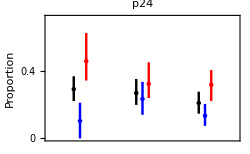
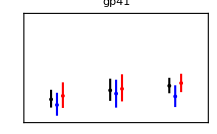
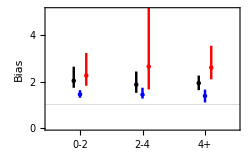
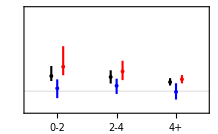

```mathematica
Column[{
Row[{PlotFigureMainText["gag","prop",nbootstraps]," ",PlotFigureMainText["gp41","prop",nbootstraps]}],
Row[{PlotFigureMainText["gag","bias",nbootstraps]," ",PlotFigureMainText["gp41","bias",nbootstraps]}]
}]
```

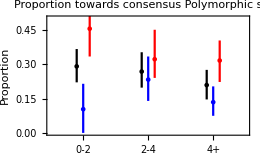
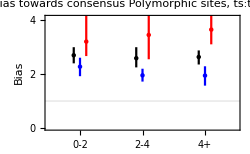
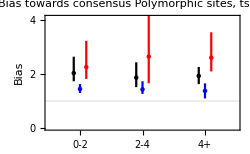
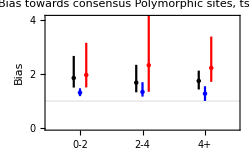
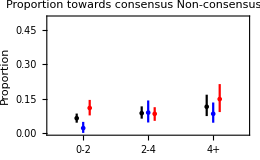
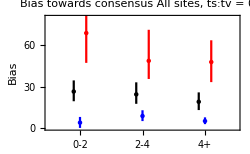
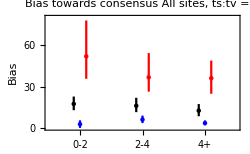
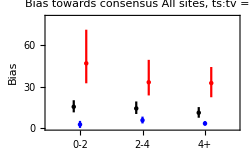
p24
-Graphics-   -Graphics-   -Graphics-   -Graphics-
   
-Graphics-   -Graphics-   -Graphics-   -Graphics-
   
gp41
-Graphics-   -Graphics-   -Graphics-   -Graphics-
   
-Graphics-   -Graphics-   -Graphics-   -Graphics-

```mathematica
Column[{
Text[Style["p24",16,Bold,FontFamily->"Ariel"]],
Row[{PlotFigureSuppl["gag",0.5,"prop",nbootstraps],"   ",PlotFigureSuppl["gag",0.5,"bias",nbootstraps],"   ",PlotFigureSuppl["gag",2,"bias",nbootstraps],"   ",PlotFigureSuppl["gag",4,"bias",nbootstraps]}],
"   ",
Row[{PlotFigureSuppl["gag",2,"NCtoC",nbootstraps],"   ",PlotFigureSuppl["gag",0.5,"biasall",nbootstraps],"   ",PlotFigureSuppl["gag",2,"biasall",nbootstraps],"   ",PlotFigureSuppl["gag",4,"biasall",nbootstraps]}],
"   ",
Text[Style["gp41",16,Bold,FontFamily->"Ariel"]],
Row[{PlotFigureSuppl["gp41",0.5,"prop",nbootstraps],"   ",PlotFigureSuppl["gp41",0.5,"bias",nbootstraps],"   ",PlotFigureSuppl["gp41",2,"bias",nbootstraps],"   ",PlotFigureSuppl["gp41",4,"bias",nbootstraps]}],
"   ",
Row[{PlotFigureSuppl["gp41",2,"NCtoC",nbootstraps],"   ",PlotFigureSuppl["gp41",0.5,"biasall",nbootstraps],"   ",PlotFigureSuppl["gp41",2,"biasall",nbootstraps],"   ",PlotFigureSuppl["gp41",4,"biasall",nbootstraps]}]}]
```

#### Draw figures: patients with high diversity at first timepoint in p24 removed

```mathematica
characterisedMutationsDir="Dropbox/Latency_in_Rakai_ms/Calculation_Evol_to_Consensus/Characterised_mutations_lowdiv_6Mar18";
```

```mathematica
nbootstraps=10000;
```

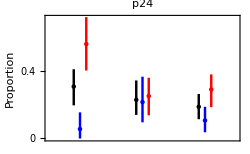
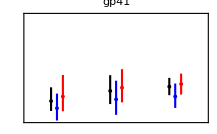
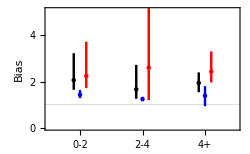
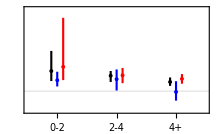

```mathematica
Column[{
Row[{PlotFigureMainText["gag","prop",nbootstraps]," ",PlotFigureMainText["gp41","prop",nbootstraps]}],
Row[{PlotFigureMainText["gag","bias",nbootstraps]," ",PlotFigureMainText["gp41","bias",nbootstraps]}]
}]
```

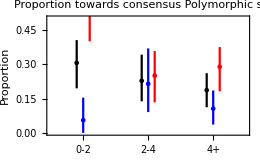
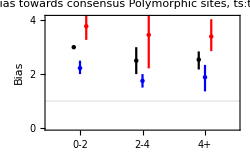
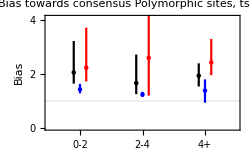
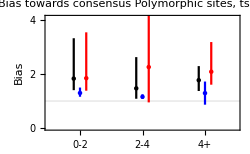
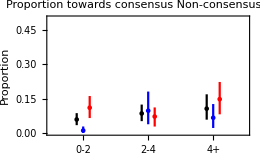
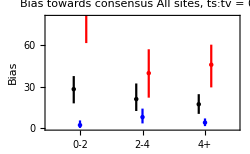
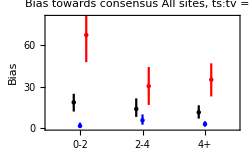
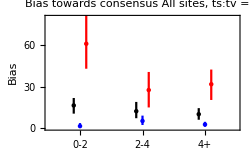
p24
-Graphics-   -Graphics-   -Graphics-   -Graphics-
   
-Graphics-   -Graphics-   -Graphics-   -Graphics-
   
gp41
-Graphics-   -Graphics-   -Graphics-   -Graphics-
   
-Graphics-   -Graphics-   -Graphics-   -Graphics-

```mathematica
Column[{
Text[Style["p24",16,Bold,FontFamily->"Ariel"]],
Row[{PlotFigureSuppl["gag",0.5,"prop",nbootstraps],"   ",PlotFigureSuppl["gag",0.5,"bias",nbootstraps],"   ",PlotFigureSuppl["gag",2,"bias",nbootstraps],"   ",PlotFigureSuppl["gag",4,"bias",nbootstraps]}],
"   ",
Row[{PlotFigureSuppl["gag",2,"NCtoC",nbootstraps],"   ",PlotFigureSuppl["gag",0.5,"biasall",nbootstraps],"   ",PlotFigureSuppl["gag",2,"biasall",nbootstraps],"   ",PlotFigureSuppl["gag",4,"biasall",nbootstraps]}],
"   ",
Text[Style["gp41",16,Bold,FontFamily->"Ariel"]],
Row[{PlotFigureSuppl["gp41",0.5,"prop",nbootstraps],"   ",PlotFigureSuppl["gp41",0.5,"bias",nbootstraps],"   ",PlotFigureSuppl["gp41",2,"bias",nbootstraps],"   ",PlotFigureSuppl["gp41",4,"bias",nbootstraps]}],
"   ",
Row[{PlotFigureSuppl["gp41",2,"NCtoC",nbootstraps],"   ",PlotFigureSuppl["gp41",0.5,"biasall",nbootstraps],"   ",PlotFigureSuppl["gp41",2,"biasall",nbootstraps],"   ",PlotFigureSuppl["gp41",4,"biasall",nbootstraps]}]}]
```

#### Draw figures: patients with high diversity at first timepoint in p24 removed and pt24 removed (high diversity in env)

```mathematica
characterisedMutationsDir="Dropbox/Latency_in_Rakai_ms/Calculation_Evol_to_Consensus/Characterised_mutations_lowdiv_nopt24_15Mar18";
```

```mathematica
nbootstraps=10000;
```

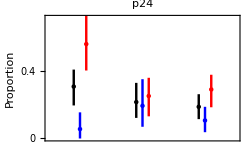
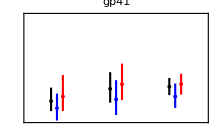
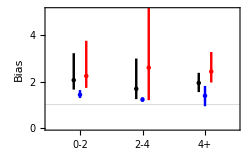
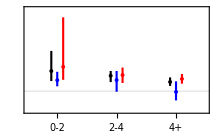

```mathematica
Column[{
Row[{PlotFigureMainText["gag","prop",nbootstraps]," ",PlotFigureMainText["gp41","prop",nbootstraps]}],
Row[{PlotFigureMainText["gag","bias",nbootstraps]," ",PlotFigureMainText["gp41","bias",nbootstraps]}]
}]
```

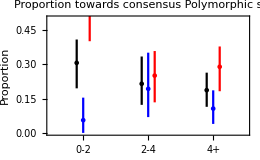
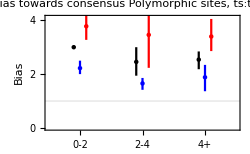
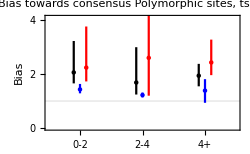
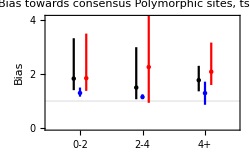
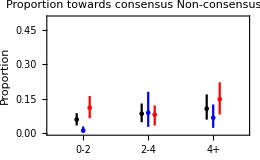
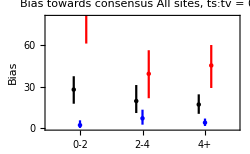
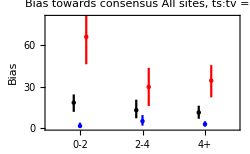
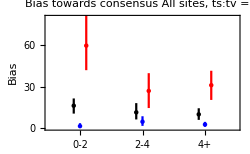
p24
-Graphics-   -Graphics-   -Graphics-   -Graphics-
   
-Graphics-   -Graphics-   -Graphics-   -Graphics-
   
gp41
-Graphics-   -Graphics-   -Graphics-   -Graphics-
   
-Graphics-   -Graphics-   -Graphics-   -Graphics-

```mathematica
Column[{
Text[Style["p24",16,Bold,FontFamily->"Ariel"]],
Row[{PlotFigureSuppl["gag",0.5,"prop",nbootstraps],"   ",PlotFigureSuppl["gag",0.5,"bias",nbootstraps],"   ",PlotFigureSuppl["gag",2,"bias",nbootstraps],"   ",PlotFigureSuppl["gag",4,"bias",nbootstraps]}],
"   ",
Row[{PlotFigureSuppl["gag",2,"NCtoC",nbootstraps],"   ",PlotFigureSuppl["gag",0.5,"biasall",nbootstraps],"   ",PlotFigureSuppl["gag",2,"biasall",nbootstraps],"   ",PlotFigureSuppl["gag",4,"biasall",nbootstraps]}],
"   ",
Text[Style["gp41",16,Bold,FontFamily->"Ariel"]],
Row[{PlotFigureSuppl["gp41",0.5,"prop",nbootstraps],"   ",PlotFigureSuppl["gp41",0.5,"bias",nbootstraps],"   ",PlotFigureSuppl["gp41",2,"bias",nbootstraps],"   ",PlotFigureSuppl["gp41",4,"bias",nbootstraps]}],
"   ",
Row[{PlotFigureSuppl["gp41",2,"NCtoC",nbootstraps],"   ",PlotFigureSuppl["gp41",0.5,"biasall",nbootstraps],"   ",PlotFigureSuppl["gp41",2,"biasall",nbootstraps],"   ",PlotFigureSuppl["gp41",4,"biasall",nbootstraps]}]}]
```